# Synthetic Lethal partner inference

```mathematica
$Path = $Path ∪ {NotebookDirectory[]};Needs["Booned`"];Needs["ActONetLib`"];
```

```mathematica
controltype=ControlDefinition
```

ControlDefinition

```mathematica
boolcolor={False-> Darker[Red,0.4],True-> Darker[Green,0.6]};
SetAttributes[CoreForm,Listable]
CoreForm[act_-> val_]:= Style[  act,val/.boolcolor,10,FontFamily->"Helvetica"]
```

## Network Analysis DISEASE → DRUG

### ⋆ Boolean Network Definition

```mathematica
F= {EGFR->!BRCA1,ERK12-> EGFR,PIK3CA->!PTEN&&EGFR,Akt->PIK3CA,GSK3->!Akt, MDM2->Akt && p53,p53->!MDM2 && (BRCA1|| !PARP1),PTEN->p53,PARP1->ERK12,BRCA1->¬CycD1,Bcl2->Akt,Bax->!Bcl2&&p53,CycD1->(!GSK3&&ERK12)||(!BRCA1&&PARP1)};
```

#### Information on network

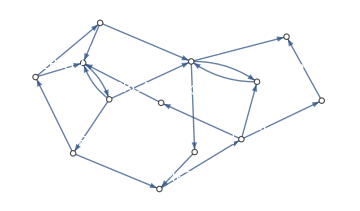
EGFR→¬BRCA1
ERK12→EGFR
PIK3CA→¬PTEN∧EGFR
Akt→PIK3CA
GSK3→¬Akt
MDM2→Akt∧p53
p53→¬MDM2∧(BRCA1∨¬PARP1)
PTEN→p53
PARP1→ERK12
BRCA1→¬CycD1
Bcl2→Akt
Bax→¬Bcl2∧p53
CycD1→(¬GSK3∧ERK12)∨(¬BRCA1∧PARP1)-Graphics-  | 1 | 2
EGFR | -Graphics3D- | -Graphics3D-
ERK12 | -Graphics3D- | -Graphics3D-
PIK3CA | -Graphics3D- | -Graphics3D-
Akt | -Graphics3D- | -Graphics3D-
GSK3 | -Graphics3D- | -Graphics3D-
MDM2 | -Graphics3D- | -Graphics3D-
p53 | -Graphics3D- | -Graphics3D-
PTEN | -Graphics3D- | -Graphics3D-
PARP1 | -Graphics3D- | -Graphics3D-
BRCA1 | -Graphics3D- | -Graphics3D-
Bcl2 | -Graphics3D- | -Graphics3D-
Bax | -Graphics3D- | -Graphics3D-
CycD1 | -Graphics3D- | -Graphics3D-
■ | ■ | ■

```mathematica
Row[{Panel@TraditionalForm@TableForm[F],ig=InteractionGraph[F,ImageSize->Medium],NiceStableStates[F]},Spacer[50]]
```

### Marking definition and satisfiability test

```mathematica
marking={CycD1->False,Bax->True}
```

{CycD1→False,Bax→True}

```mathematica
markers=First/@marking
```

{CycD1,Bax}

```mathematica
sys=StabilityCondition[F]/.marking; isat=SatisfiableQ[sys];
```

```mathematica
TableForm[{NiceStableStates[marking], Panel[Row[{Style["Satisfiable system","Helvetica",14],Checkbox[isat, Enabled->False]},"  "]]}, TableAlignments->Center]
```

| 1
CycD1 | -Graphics3D-
Bax | -Graphics3D-
■ | ■
    Satisfiable system

### List of variables that are allowed to be frozen either True or False

By definition  the markers cannot be frozen

```mathematica
frozenfalse=Complement[Agents[F],markers]
```

{Akt,Bcl2,BRCA1,EGFR,ERK12,GSK3,MDM2,p53,PARP1,PIK3CA,PTEN}

```mathematica
frozentrue=Complement[Agents[F],markers]
```

{Akt,Bcl2,BRCA1,EGFR,ERK12,GSK3,MDM2,p53,PARP1,PIK3CA,PTEN}

### Core

Computation of the core

```mathematica
Highlighted[TableForm[Timing[Column@CoreForm[cores=Destify[F,!MarkingToFormula[marking],Nothing,frozenfalse,frozentrue, ControlType-> controltype]]]],Frame-> True]
```

1.96561
{BRCA1}
{p53}
{Akt}
{Bcl2}
{MDM2}
{PIK3CA}
{GSK3,EGFR}
{GSK3,ERK12}
{PTEN,EGFR}

## Validation of the solutions

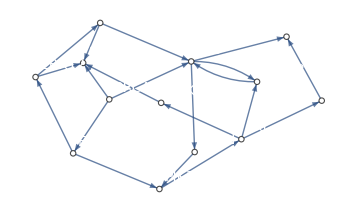
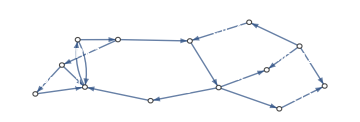
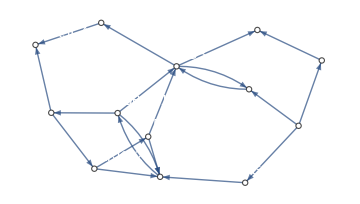
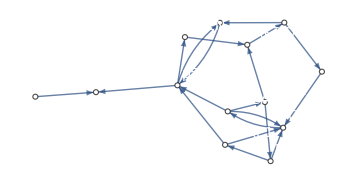
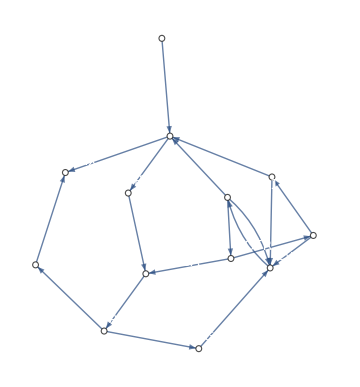
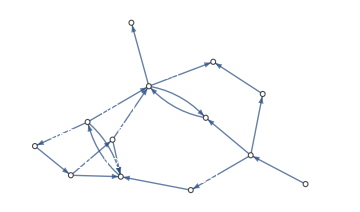
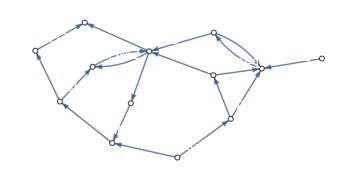
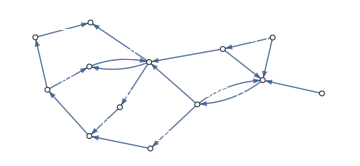
EGFR→!BRCA1
ERK12→EGFR
PIK3CA→!PTEN&&EGFR
Akt→PIK3CA
GSK3→!Akt
MDM2→Akt&&p53
p53→!MDM2&&(BRCA1||!PARP1)
PTEN→p53
PARP1→ERK12
BRCA1→False
Bcl2→Akt
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1
EGFR | -Graphics3D-
ERK12 | -Graphics3D-
PIK3CA | -Graphics3D-
Akt | -Graphics3D-
GSK3 | -Graphics3D-
MDM2 | -Graphics3D-
p53 | -Graphics3D-
PTEN | -Graphics3D-
PARP1 | -Graphics3D-
BRCA1 | -Graphics3D-
Bcl2 | -Graphics3D-
Bax | -Graphics3D-
CycD1 | -Graphics3D-
■ | ■{BRCA1→False}
EGFR→!BRCA1
ERK12→EGFR
PIK3CA→!PTEN&&EGFR
Akt→PIK3CA
GSK3→!Akt
MDM2→Akt&&p53
p53→False
PTEN→p53
PARP1→ERK12
BRCA1→!CycD1
Bcl2→Akt
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1 | 2
EGFR | -Graphics3D- | -Graphics3D-
ERK12 | -Graphics3D- | -Graphics3D-
PIK3CA | -Graphics3D- | -Graphics3D-
Akt | -Graphics3D- | -Graphics3D-
GSK3 | -Graphics3D- | -Graphics3D-
MDM2 | -Graphics3D- | -Graphics3D-
p53 | -Graphics3D- | -Graphics3D-
PTEN | -Graphics3D- | -Graphics3D-
PARP1 | -Graphics3D- | -Graphics3D-
BRCA1 | -Graphics3D- | -Graphics3D-
Bcl2 | -Graphics3D- | -Graphics3D-
Bax | -Graphics3D- | -Graphics3D-
CycD1 | -Graphics3D- | -Graphics3D-
■ | ■ | ■{p53→False}
EGFR→!BRCA1
ERK12→EGFR
PIK3CA→!PTEN&&EGFR
Akt→True
GSK3→!Akt
MDM2→Akt&&p53
p53→!MDM2&&(BRCA1||!PARP1)
PTEN→p53
PARP1→ERK12
BRCA1→!CycD1
Bcl2→Akt
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1
EGFR | -Graphics3D-
ERK12 | -Graphics3D-
PIK3CA | -Graphics3D-
Akt | -Graphics3D-
GSK3 | -Graphics3D-
MDM2 | -Graphics3D-
p53 | -Graphics3D-
PTEN | -Graphics3D-
PARP1 | -Graphics3D-
BRCA1 | -Graphics3D-
Bcl2 | -Graphics3D-
Bax | -Graphics3D-
CycD1 | -Graphics3D-
■ | ■{Akt→True}
EGFR→!BRCA1
ERK12→EGFR
PIK3CA→!PTEN&&EGFR
Akt→PIK3CA
GSK3→!Akt
MDM2→Akt&&p53
p53→!MDM2&&(BRCA1||!PARP1)
PTEN→p53
PARP1→ERK12
BRCA1→!CycD1
Bcl2→True
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1 | 2
EGFR | -Graphics3D- | -Graphics3D-
ERK12 | -Graphics3D- | -Graphics3D-
PIK3CA | -Graphics3D- | -Graphics3D-
Akt | -Graphics3D- | -Graphics3D-
GSK3 | -Graphics3D- | -Graphics3D-
MDM2 | -Graphics3D- | -Graphics3D-
p53 | -Graphics3D- | -Graphics3D-
PTEN | -Graphics3D- | -Graphics3D-
PARP1 | -Graphics3D- | -Graphics3D-
BRCA1 | -Graphics3D- | -Graphics3D-
Bcl2 | -Graphics3D- | -Graphics3D-
Bax | -Graphics3D- | -Graphics3D-
CycD1 | -Graphics3D- | -Graphics3D-
■ | ■ | ■{Bcl2→True}
EGFR→!BRCA1
ERK12→EGFR
PIK3CA→!PTEN&&EGFR
Akt→PIK3CA
GSK3→!Akt
MDM2→True
p53→!MDM2&&(BRCA1||!PARP1)
PTEN→p53
PARP1→ERK12
BRCA1→!CycD1
Bcl2→Akt
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1 | 2
EGFR | -Graphics3D- | -Graphics3D-
ERK12 | -Graphics3D- | -Graphics3D-
PIK3CA | -Graphics3D- | -Graphics3D-
Akt | -Graphics3D- | -Graphics3D-
GSK3 | -Graphics3D- | -Graphics3D-
MDM2 | -Graphics3D- | -Graphics3D-
p53 | -Graphics3D- | -Graphics3D-
PTEN | -Graphics3D- | -Graphics3D-
PARP1 | -Graphics3D- | -Graphics3D-
BRCA1 | -Graphics3D- | -Graphics3D-
Bcl2 | -Graphics3D- | -Graphics3D-
Bax | -Graphics3D- | -Graphics3D-
CycD1 | -Graphics3D- | -Graphics3D-
■ | ■ | ■{MDM2→True}
EGFR→!BRCA1
ERK12→EGFR
PIK3CA→True
Akt→PIK3CA
GSK3→!Akt
MDM2→Akt&&p53
p53→!MDM2&&(BRCA1||!PARP1)
PTEN→p53
PARP1→ERK12
BRCA1→!CycD1
Bcl2→Akt
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1
EGFR | -Graphics3D-
ERK12 | -Graphics3D-
PIK3CA | -Graphics3D-
Akt | -Graphics3D-
GSK3 | -Graphics3D-
MDM2 | -Graphics3D-
p53 | -Graphics3D-
PTEN | -Graphics3D-
PARP1 | -Graphics3D-
BRCA1 | -Graphics3D-
Bcl2 | -Graphics3D-
Bax | -Graphics3D-
CycD1 | -Graphics3D-
■ | ■{PIK3CA→True}
EGFR→True
ERK12→EGFR
PIK3CA→!PTEN&&EGFR
Akt→PIK3CA
GSK3→False
MDM2→Akt&&p53
p53→!MDM2&&(BRCA1||!PARP1)
PTEN→p53
PARP1→ERK12
BRCA1→!CycD1
Bcl2→Akt
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1
EGFR | -Graphics3D-
ERK12 | -Graphics3D-
PIK3CA | -Graphics3D-
Akt | -Graphics3D-
GSK3 | -Graphics3D-
MDM2 | -Graphics3D-
p53 | -Graphics3D-
PTEN | -Graphics3D-
PARP1 | -Graphics3D-
BRCA1 | -Graphics3D-
Bcl2 | -Graphics3D-
Bax | -Graphics3D-
CycD1 | -Graphics3D-
■ | ■{GSK3→False,EGFR→True}
EGFR→!BRCA1
ERK12→True
PIK3CA→!PTEN&&EGFR
Akt→PIK3CA
GSK3→False
MDM2→Akt&&p53
p53→!MDM2&&(BRCA1||!PARP1)
PTEN→p53
PARP1→ERK12
BRCA1→!CycD1
Bcl2→Akt
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1
EGFR | -Graphics3D-
ERK12 | -Graphics3D-
PIK3CA | -Graphics3D-
Akt | -Graphics3D-
GSK3 | -Graphics3D-
MDM2 | -Graphics3D-
p53 | -Graphics3D-
PTEN | -Graphics3D-
PARP1 | -Graphics3D-
BRCA1 | -Graphics3D-
Bcl2 | -Graphics3D-
Bax | -Graphics3D-
CycD1 | -Graphics3D-
■ | ■{GSK3→False,ERK12→True}
EGFR→True
ERK12→EGFR
PIK3CA→!PTEN&&EGFR
Akt→PIK3CA
GSK3→!Akt
MDM2→Akt&&p53
p53→!MDM2&&(BRCA1||!PARP1)
PTEN→False
PARP1→ERK12
BRCA1→!CycD1
Bcl2→Akt
Bax→!Bcl2&&p53
CycD1→(!GSK3&&ERK12)||(!BRCA1&&PARP1)
-Graphics-  | 1
EGFR | -Graphics3D-
ERK12 | -Graphics3D-
PIK3CA | -Graphics3D-
Akt | -Graphics3D-
GSK3 | -Graphics3D-
MDM2 | -Graphics3D-
p53 | -Graphics3D-
PTEN | -Graphics3D-
PARP1 | -Graphics3D-
BRCA1 | -Graphics3D-
Bcl2 | -Graphics3D-
Bax | -Graphics3D-
CycD1 | -Graphics3D-
■ | ■{PTEN→False,EGFR→True}

```mathematica
TableForm[Function[sol, With[{Fres=ActNet[F,sol]},
Panel[Column[
{
Column[Fres],
Row[{InteractionGraph[Fres,ImageSize-> Medium],NiceStableStates[Fres]},Spacer[20]]
}],Style[sol, FontFamily->"Calibri Light",FontSize->14,FontColor -> White,Background->If[¬SatisfiableQ[StabilityCondition[Fres]/.marking],GrayLevel[0.4],Red]]
,
Alignment->{Top,Center}]
]]/@cores]
```